```mathematica
code:=Module[{
func=RandomChoice[{a,b,c,f,g,s,p,r,y,A,B,C,F,G,P,R,Y}],
variable=RandomChoice[{x,z,t,n,k,w,u,v,θ,ψ}]},
P1 = {0,0};
P2={0,0};
P3={0,0};
P4={.5,Random[Integer,{-4,4}]};
P5={3.5,Random[Integer,{-4,4}]};
P6={-3.5,Random[Integer,{-4,4}]};
While[
P1[[1]]==P2[[1]]||P1[[1]]==P3[[1]]||P2[[1]]==P3[[1]],
P1 = {Random[Integer,{-4,4}], Random[Integer,{-4,4}]};
P2={Random[Integer,{-4,4}], Random[Integer,{-4,4}]};
P3={Random[Integer,{-4,4}], Random[Integer,{-4,4}]}];
ff[xx_]=InterpolatingPolynomial[{P1,P2,P3,P4,P5,P6},xx];
mm=First[xx/.Solve[ff'[xx]==0,xx]];
StringJoin["\\begin{question}
In the plot below, is $",ToString[TeXForm[func]],"$ a function of $",ToString[TeXForm[variable]],"$?
\\[
\\begin{tikzpicture}
\\begin{axis}[
            ymin=-5,
			ymax=5,
            axis lines =center, xlabel=$",ToString[TeXForm[variable]],"$, ylabel=$",ToString[TeXForm[func]],"$,
              every axis y label/.style={at=(current axis.above origin),anchor=south},
              every axis x label/.style={at=(current axis.right of origin),anchor=west},
            domain=-5:5,
            grid = major,
          ]
          \\addplot [very thick, smooth] {",ToString[InputForm[ff[x]]],"};
        \\end{axis}
\\end{tikzpicture}
\\]
\\begin{multiple-choice}
\\choice[correct]{Yes.}
\\choice{No.}
\\end{multiple-choice}
\\begin{solution}
\\begin{hint}
For each input, how many outputs are there?
\\end{hint}
\\end{solution}
Use the plot to compute $",ToString[TeXForm[func]],"(",ToString[P1[[1]]],")$
\\begin{solution}
\\begin{hint}
To start, find $",ToString[P1[[1]]],"$ on the horizontal axis. 
\\end{hint}
\\begin{hint}
Now from this position, move up or down until you reach the curve. The value of $",ToString[TeXForm[func]],"(",ToString[P1[[1]]],")$ is the height of the curve at the point $", ToString[TeXForm[variable]],"=",ToString[P1[[1]]],"$.
\\end{hint}
The value of $",ToString[TeXForm[func]],"(",ToString[P1[[1]]],")$ is \\answer{$",ToString[P1[[2]]],"$}.
\\end{solution}
Is $",ToString[TeXForm[func]],"^{-1}$ a function of $",ToString[TeXForm[variable]],"$ on the domain $[",ToString[Ceiling[MinValue[{ff[xx],-5≤ xx≤ 5},xx]]],",",ToString[Floor[MaxValue[{ff[xx],-5≤ xx≤ 5},xx]]],"]$?
\\begin{multiple-choice}",If[-5≤mm≤5,StringJoin[
"
\\choice{Yes.}
\\choice[correct]{No.}
\\end{multiple-choice}
\\begin{solution}
\\begin{hint}
For each input of $",ToString[TeXForm[func]],"^{-1}$, how many outputs are there?
\\end{hint}
\\end{solution}
Restrict the domain of $",ToString[TeXForm[func]],"$ to ",If[mm>P2[[1]], StringJoin["$[-5,",ToString[Floor[mm]],"]$"],StringJoin["$[",ToString[Ceiling[mm]],",5]$"]]," and compute $",ToString[TeXForm[func]],"^{-1}(",ToString[P2[[1]]],")$.
\\begin{solution}
\\begin{hint}
Since we are looking at $",ToString[TeXForm[func]],"^{-1}$, now we must find $",ToString[P2[[2]]],"$ on the vertical axis. 
\\end{hint}
The value of $",ToString[TeXForm[func]],"^{-1}(",ToString[P2[[2]]],")$ is \\answer{$",ToString[P2[[1]]],"$}.
\\end{solution}
\\end{question}
"],StringJoin["
\\choice[correct]{Yes.}
\\choice{No.}
\\end{multiple-choice}
\\begin{solution}
\\begin{hint}
For each input of $",ToString[TeXForm[func]],"^{-1}$, how many outputs are there?
\\end{hint}
\\end{solution}
Compute $",ToString[TeXForm[func]],"^{-1}(",ToString[P2[[1]]],")$.
\\begin{solution}
\\begin{hint}
Since we are looking at $",ToString[TeXForm[func]],"^{-1}$, now we must find $",ToString[P2[[2]]],"$ on the vertical axis. 
\\end{hint}
The value of $",ToString[TeXForm[func]],"^{-1}(",ToString[P2[[2]]],")$ is \\answer{$",ToString[P2[[1]]],"$}.
\\end{solution}
\\end{question}
"]
]]
]
```

\begin{question}
In the plot below, is $r$ a function of $t$?
\[
\begin{tikzpicture}
\begin{axis}[
            ymin=-5,
			ymax=5,
            axis lines =center, xlabel=$t$, ylabel=$r$,
              every axis y label/.style={at=(current axis.above origin),anchor=south},
              every axis x label/.style={at=(current axis.right of origin),anchor=west},
            domain=-5:5,
            grid = major,
          ]
          \addplot [very thick, smooth] {4 + (-4 + x)*(3.5 + x)*(0.2857142857142857 + (-0.5 + x)*(-0.19047619047619047 + (-2 + x)*(0.059863945578231284 + 0.07870225013082155*(3 + x))))};
        \end{axis}
\end{tikzpicture}
\]
\begin{multiple-choice}
\choice[correct]{Yes.}
\choice{No.}
\end{multiple-choice}
\begin{solution}
\begin{hint}
For each input, how many outputs are there?
\end{hint}
\end{solution}
Use the plot to compute $r(4)$
\begin{solution}
\begin{hint}
To start, find $4$ on the horizontal axis. 
\end{hint}
\begin{hint}
Now from this position, move up or down until you reach the curve. The value of $r(4)$ is the height of the curve at the point $t=4$.
\end{hint}
The value of $r(4)$ is \answer{$4$}.
\end{solution}
Is $r^{-1}$ a function of $t$ on the domain $[-28,78]$?
\begin{multiple-choice}
\choice{Yes.}
\choice[correct]{No.}
\end{multiple-choice}
\begin{solution}
\begin{hint}
For each input of $r^{-1}$, how many outputs are there?
\end{hint}
\end{solution}
Restrict the domain of $r$ to $[-3,5]$ and compute $r^{-1}(2)$.
\begin{solution}
\begin{hint}
Since we are looking at $r^{-1}$, now we must find $4$ on the vertical axis. 
\end{hint}
The value of $r^{-1}(4)$ is \answer{$2$}.
\end{solution}
\end{question}
\begin{question}
In the plot below, is $y$ a function of $v$?
\[
\begin{tikzpicture}
\begin{axis}[
            ymin=-5,
			ymax=5,
            axis lines =center, xlabel=$v$, ylabel=$y$,
              every axis y label/.style={at=(current axis.above origin),anchor=south},
              every axis x label/.style={at=(current axis.right of origin),anchor=west},
            domain=-5:5,
            grid = major,
          ]
          \addplot [very thick, smooth] {-1 + (3.5 + x)*(0.14285714285714285 + (-3.5 + x)*(0.12244897959183673 + x*(-0.3166357452071738 + (-2 + x)*(-0.09053803339517619 + 0.1527932385075242*(3 + x)))))};
        \end{axis}
\end{tikzpicture}
\]
\begin{multiple-choice}
\choice[correct]{Yes.}
\choice{No.}
\end{multiple-choice}
\begin{solution}
\begin{hint}
For each input, how many outputs are there?
\end{hint}
\end{solution}
Use the plot to compute $y(-3)$
\begin{solution}
\begin{hint}
To start, find $-3$ on the horizontal axis. 
\end{hint}
\begin{hint}
Now from this position, move up or down until you reach the curve. The value of $y(-3)$ is the height of the curve at the point $v=-3$.
\end{hint}
The value of $y(-3)$ is \answer{$0$}.
\end{solution}
Is $y^{-1}$ a function of $v$ on the domain $[-156,198]$?
\begin{multiple-choice}
\choice{Yes.}
\choice[correct]{No.}
\end{multiple-choice}
\begin{solution}
\begin{hint}
For each input of $y^{-1}$, how many outputs are there?
\end{hint}
\end{solution}
Restrict the domain of $y$ to $[-3,5]$ and compute $y^{-1}(2)$.
\begin{solution}
\begin{hint}
Since we are looking at $y^{-1}$, now we must find $4$ on the vertical axis. 
\end{hint}
The value of $y^{-1}(4)$ is \answer{$2$}.
\end{solution}
\end{question}
\begin{question}
In the plot below, is $y$ a function of $n$?
\[
\begin{tikzpicture}
\begin{axis}[
            ymin=-5,
			ymax=5,
            axis lines =center, xlabel=$n$, ylabel=$y$,
              every axis y label/.style={at=(current axis.above origin),anchor=south},
              every axis x label/.style={at=(current axis.right of origin),anchor=west},
            domain=-5:5,
            grid = major,
          ]
          \addplot [very thick, smooth] {-4 + (4 + x)*(1 + (-4 + x)*(0.15873015873015872 + (-0.5 + x)*(0.09682539682539684 + (-0.019143819143819147 + 0.007696007696007697*(-3.5 + x))*(2 + x))))};
        \end{axis}
\end{tikzpicture}
\]
\begin{multiple-choice}
\choice[correct]{Yes.}
\choice{No.}
\end{multiple-choice}
\begin{solution}
\begin{hint}
For each input, how many outputs are there?
\end{hint}
\end{solution}
Use the plot to compute $y(-4)$
\begin{solution}
\begin{hint}
To start, find $-4$ on the horizontal axis. 
\end{hint}
\begin{hint}
Now from this position, move up or down until you reach the curve. The value of $y(-4)$ is the height of the curve at the point $n=-4$.
\end{hint}
The value of $y(-4)$ is \answer{$-4$}.
\end{solution}
Is $y^{-1}$ a function of $n$ on the domain $[-20,8]$?
\begin{multiple-choice}
\choice{Yes.}
\choice[correct]{No.}
\end{multiple-choice}
\begin{solution}
\begin{hint}
For each input of $y^{-1}$, how many outputs are there?
\end{hint}
\end{solution}
Restrict the domain of $y$ to $[-2,5]$ and compute $y^{-1}(-2)$.
\begin{solution}
\begin{hint}
Since we are looking at $y^{-1}$, now we must find $-1$ on the vertical axis. 
\end{hint}
The value of $y^{-1}(-1)$ is \answer{$-2$}.
\end{solution}
\end{question}
\begin{question}
In the plot below, is $R$ a function of $u$?
\[
\begin{tikzpicture}
\begin{axis}[
            ymin=-5,
			ymax=5,
            axis lines =center, xlabel=$u$, ylabel=$R$,
              every axis y label/.style={at=(current axis.above origin),anchor=south},
              every axis x label/.style={at=(current axis.right of origin),anchor=west},
            domain=-5:5,
            grid = major,
          ]
          \addplot [very thick, smooth] {1 + (-4 + x)*(0.4 + (3.5 + x)*(0.1 + x*(0.016666666666666666 + (-0.011193568336425479 - 0.005318491032776748*(-3.5 + x))*(2 + x))))};
        \end{axis}
\end{tikzpicture}
\]
\begin{multiple-choice}
\choice[correct]{Yes.}
\choice{No.}
\end{multiple-choice}
\begin{solution}
\begin{hint}
For each input, how many outputs are there?
\end{hint}
\end{solution}
Use the plot to compute $R(0)$
\begin{solution}
\begin{hint}
To start, find $0$ on the horizontal axis. 
\end{hint}
\begin{hint}
Now from this position, move up or down until you reach the curve. The value of $R(0)$ is the height of the curve at the point $u=0$.
\end{hint}
The value of $R(0)$ is \answer{$-2$}.
\end{solution}
Is $R^{-1}$ a function of $u$ on the domain $[-2,4]$?
\begin{multiple-choice}
\choice{Yes.}
\choice[correct]{No.}
\end{multiple-choice}
\begin{solution}
\begin{hint}
For each input of $R^{-1}$, how many outputs are there?
\end{hint}
\end{solution}
Restrict the domain of $R$ to $[-2,5]$ and compute $R^{-1}(-2)$.
\begin{solution}
\begin{hint}
Since we are looking at $R^{-1}$, now we must find $-2$ on the vertical axis. 
\end{hint}
The value of $R^{-1}(-2)$ is \answer{$-2$}.
\end{solution}
\end{question}

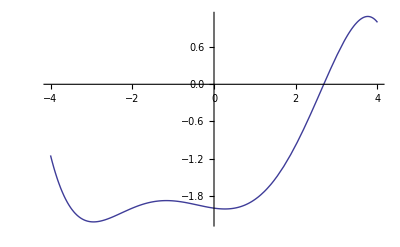

```mathematica
StringJoin[Table[code,{i,1,4}]]
Plot[ff[xx],{xx,-4,4}]
```